```mathematica
(* ===YOUR RunCatMap (color,unchanged)===*)RunCatMap[image_,imageSize_,iterations_,a_,b_]:=Module[{catMap,redChannel,greenChannel,blueChannel},catMap=Compile[{{pic,_Integer,2}},Table[pic[[Mod[x+a*y,imageSize,1],Mod[b*x+(1+a*b)*y,imageSize,1]]],{x,imageSize},{y,imageSize}]];
{redChannel,greenChannel,blueChannel}=ColorSeparate[image];
redChannel=Image[Nest[catMap,ImageData[redChannel,"Byte"],iterations],"Byte"];
greenChannel=Image[Nest[catMap,ImageData[greenChannel,"Byte"],iterations],"Byte"];
blueChannel=Image[Nest[catMap,ImageData[blueChannel,"Byte"],iterations],"Byte"];
ColorCombine[{redChannel,greenChannel,blueChannel}]]

(* ===PERIOD COMPUTATION (matrix power method)===*)
ArnoldPeriod[N_]:=Module[{k=1,A={{1,1},{1,2}}},While[Mod[MatrixPower[A,k],N]!=IdentityMatrix[2],k++];k]

(* ===YOUR MyMSSIM===*)
MyMSSIM[img1raw_Image,img2raw_Image,window_:GaussianMatrix[{Table[(11-1)/2,{2}],1.5},Method->"Gaussian"],k1_:0.01,k2_:0.03]:=Module[{f=Max[1,Round[Min[Sequence@@ImageDimensions[img1raw]]/256]],img1in=ColorConvert[Image[img1raw,"Real"],"Grayscale"],img2in=ColorConvert[Image[img2raw,"Real"],"Grayscale"],mssimmap,mssim},If[f>1,{img1in,img2in}=ImageCorrelate[ImagePad[#,NestList[Reverse,{Floor[(f-1)/2],Ceiling[(f-1)/2]},1],"Reversed"],ConstantArray[1./Times[f,f],{f,f}],Padding->None]&/@{img1in,img2in};
{img1in,img2in}=ImageTake[#,{1,-1,f},{1,-1,f}]&/@{img1in,img2in};];
mssimmap=Function[{img1,img2},Function[{mu1,mu2},Function[{mu1mu1,mu2mu2,mu1mu2},ImageApply[#1/#2&,{ImageMultiply[ImageAdd[ImageMultiply[mu1mu2,2.],k1^2],ImageAdd[ImageMultiply[ImageSubtract[ImageCorrelate[ImageMultiply[img1,img2],window,Padding->None],mu1mu2],2.],k2^2]],ImageMultiply[ImageAdd[ImageAdd[mu1mu1,mu2mu2],k1^2],ImageAdd[ImageAdd[ImageSubtract[ImageCorrelate[ImageMultiply[img1,img1],window,Padding->None],mu1mu1],ImageSubtract[ImageCorrelate[ImageMultiply[img2,img2],window,Padding->None],mu2mu2]],k2^2]]}]][ImageMultiply[mu1,mu1],ImageMultiply[mu2,mu2],ImageMultiply[mu1,mu2]]][ImageCorrelate[img1,window,Padding->None],ImageCorrelate[img2,window,Padding->None]]][img1in,img2in];
mssim=ImageMeasurements[mssimmap,"Mean"];
Return[mssim];];
```

Images resized to 256×256.

Period P = 192

Testing 97 iteration values per image.

--- Mandrill ---

Optimal k* = 174 (k*/P = 0.906)

Minimum MSSIM = 0.0224

--- Peppers ---

Optimal k* = 60 (k*/P = 0.313)

Minimum MSSIM = 0.0143

Displaying images and MSSIM plots ...

Mandrill:

-Graphics-

Peppers:

-Graphics-

MSSIM plots:

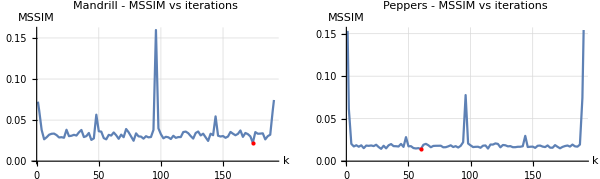

------------------------------------------------------------

SUMMARY

------------------------------------------------------------

Image      | Optimal k* | k*/P     | Minimum MSSIM

-----------|------------|----------|-------------

Mandrill   |        174 |    0.906 |     0.0224

Peppers    |         60 |    0.313 |     0.0143

------------------------------------------------------------

```mathematica
(* ===MAIN ANALYSIS===*)
n=256;a=1;b=1;
imgMandrill=ExampleData[{"TestImage","Mandrill"}];
imgPeppers=ExampleData[{"TestImage","Peppers"}];
imgMandrill=ImageResize[imgMandrill,{n,n}];
imgPeppers=ImageResize[imgPeppers,{n,n}];
Print["Images resized to ",n,"×",n,"."];
P=ArnoldPeriod[n];
Print["Period P = ",P];
step=Max[1,Floor[P/80]];
ks=Sort[DeleteDuplicates[Join[{1},Range[2,P-1,step],{Floor[P/2],P-1}]]];
Print["Testing ",Length[ks]," iteration values per image."];

analyseImage[img_,name_]:=Module[{ssims,bestIdx,kOpt,imgWeak,imgOpt,plot},Print["\n--- ",name," ---"];
ssims=Table[transformed=RunCatMap[img,n,k,a,b];MyMSSIM[img,transformed],{k,ks}];
bestIdx=Ordering[ssims,1][[1]];
kOpt=ks[[bestIdx]];
Print["Optimal k* = ",kOpt," (k*/P = ",NumberForm[N[kOpt/P],{4,3}],")"];
Print["Minimum MSSIM = ",NumberForm[ssims[[bestIdx]],{6,4}]];
imgWeak=RunCatMap[img,n,1,a,b];
imgOpt=RunCatMap[img,n,kOpt,a,b];
plot=ListLinePlot[Transpose[{ks,ssims}],PlotLabel->name<>" - MSSIM vs iterations",AxesLabel->{"k","MSSIM"},Epilog->{Red,PointSize[Large],Point[{kOpt,ssims[[bestIdx]]}]},GridLines->Automatic, PlotRange->All];
{plot,imgWeak,imgOpt,ks,ssims,kOpt,name}];

{mPlot,mWeak,mOpt,mKs,mSsims,mKopt,mName}=analyseImage[imgMandrill,"Mandrill"];
{pPlot,pWeak,pOpt,pKs,pSsims,pKopt,pName}=analyseImage[imgPeppers,"Peppers"];

Print["\nDisplaying images and MSSIM plots ..."];
Print["Mandrill:"];
GraphicsGrid[{{imgMandrill,mWeak,mOpt}},ImageSize->600]
Print["Peppers:"];
GraphicsGrid[{{imgPeppers,pWeak,pOpt}},ImageSize->600]
Print["MSSIM plots:"];
GraphicsGrid[{{mPlot,pPlot}},ImageSize->600]

(* ===CORRECTED SUMMARY===*)
Print["\n",StringRepeat["-",60]];
Print["SUMMARY"];
Print[StringRepeat["-",60]];
Print["Image      | Optimal k* | k*/P     | Minimum MSSIM"];
Print["-----------|------------|----------|-------------"];

(*Helper to format numbers as strings with fixed width*)
fmtNum[num_,width_,prec_]:=StringPadLeft[ToString[NumberForm[num,{prec,prec}]],width];
fmtInt[int_,width_]:=StringPadLeft[ToString[int],width];

Print[StringJoin["Mandrill   | ",fmtInt[mKopt,10]," | ",fmtNum[N[mKopt/P],8,3]," | ",fmtNum[Min[mSsims],10,4]]];
Print[StringJoin["Peppers    | ",fmtInt[pKopt,10]," | ",fmtNum[N[pKopt/P],8,3]," | ",fmtNum[Min[pSsims],10,4]]];
Print[StringRepeat["-",60]];
```